```mathematica
(*Soil Moisture PDF based on Numerical estimation of the normalization constant*)
Clear[pz,pzm,χPDF,χIavgN1,aλ,aPET, pzm, pz,pqm,PQm,σ2Qm,aλ,pχ,CC1N,ϑ]
(*Rainfall PDF, exponential and mixed exponential*)
pz[z_,γ_]:=γ ⅇ^(-γ z)UnitStep[z]
pzm[z_,ω_,γ1_,γ2_]:=(ω γ1 ⅇ^(-γ1 z)+(1-ω)γ2 ⅇ^(-γ2 z))UnitStep[z]
(*Soil Moisture (zero) top layer PDF *)
(*N1[DI_?NumericQ,γ_?NumericQ]:=N1[DI,γ]=1/NIntegrate[ⅇ^(-γ x0)x0^(γ/DI-1),{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)
χPDF[x0_?NumericQ,DI_?NumericQ,γ_?NumericQ]:=χPDF[x0,DI,γ]=(γ^(γ/DI)/Gamma[γ/DI,0,γ]) ⅇ^(-γ x0)x0^(γ/DI-1)(*UnitStep[1-x0]UnitStep[x0]*)
χIavg[DI_?NumericQ,γ_?NumericQ]:=χIavg[DI,γ]= (1/DI-(γ^(γ/DI-1)ⅇ^-γ)/Gamma[γ/DI,0,γ])

(*Average based on the numerical PDF*)(*DI=(γ k)/λ*)
(*χIavgN[DI_?NumericQ,γ_?NumericQ]:=χIavgN[DI,γ]=NIntegrate[x0 χPDF[x0,DI,γ],{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)

χIavgN1[DI_?NumericQ,γ_?NumericQ]:=χIavgN1[DI,γ]=UnitStep[χIavg[DI,γ]-1]+UnitStep[1-χIavg[DI,γ]]χIavg[DI,γ]

(*frequency Adjustment*)
(*Based on probability of rainfall normalized exceeding average soil spare storage capacity*)
(*PET/(α λ) α/w PDF(x=1)*)
(*PET/(α λ) α/w PDF(x=1)*)
aλ[DI_?NumericQ,γ1_?NumericQ]:=aλ[DI,γ1]=DI/γ1 χPDF[1,DI,γ1]UnitStep[1-DI/γ1 χPDF[1,DI,γ1]]+UnitStep[DI/γ1 χPDF[1,DI,γ1]-1](*ⅇ^(-(1-χIavgN[DI,γ1,0,0])γ1)*)
aPET[DI_?NumericQ,γ1_?NumericQ]:=aPET[DI,γ1]=(1-χIavg[DI,γ1])(*(1-(ⅇ^(10(DI-1))/(1+ⅇ^(10(DI-1)))))*)
(**)
ξ1=2.0; (*3.5 Lower Number Lowers Curve*)
ξ2=2.0; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.0;
ϑold[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=ϑ[LI,γs,β]=Max[-LI/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)LI/(γs^(1-.5 β^2))),0]
ξ1n=2;
ξ2n=0.5;
ξ3n=2.75;
ξ4n=-16.29;
ξ5n=-0.2;
ξ6n=0.566;
ξ7n=-1.352;
ξ8n=5;
ξ9n=57.1;
ξ10n=2.66;
(*(1+ξ5n +ξ6n β^1.5)*)
ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=Piecewise[{{Max[ⅇ^(-2(1-ξ1n β^2)LI/(γs^(1-β^2/2)))-(ξ2n+ξ3n β+ξ4n β^4.5)LI/(γs^(2(1-ξ1n β^2))),0],0<=β<=.5},{Max[ⅇ^(-LI/γs^(7/8))-(ξ7n+ξ8n β+ξ9n β^13.5)(LI/γs)^(1+ξ5n +ξ6n β^1.5),0],.5<β<1},{Max[ⅇ^(-LI/γs)-LI/γs ξ10n,0],β==1}}]
(*(DI aPET+BI)/aλ*)
(*First Moment--the Mean*)
CC1[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1[LI,γs,β,ϑ]=Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]/(Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI])(1/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
(*Take the LOg and then exp to avoid a really small number in the denominator beyond the precision of the computer*)
CC1N[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1N[LI,γs,β,ϑ]=Exp[Evaluate[Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]]]]
pχ[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχ[x,LI,γs,β,ϑ]=CC1[LI,γs,β,ϑ]((1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/LI)
pχPlot[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχPlot[x,LI,γs,β,ϑ]=(*CC1N[LI,γs,β,ϑ] *)Exp[Evaluate[Max[Log[(1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))]+Log[(1-x)^((γs (1-ϑ))/(1-β ϑ))]-Log[(x^(1-γs/LI))]+Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]],-700]]]
(**)
χavg[LI_,γs_,β_,ϑ_]:=γs/(γs+LI(1+γs(1-ϑ)/(1-ϑ β)))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),1+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+2+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
(*Average of the square of soil moisture*)
χ2avg[LI_,γs_,β_,ϑ_]:=((γs(LI+γs))/((γs+LI(1+γs(1-ϑ)/(1-ϑ β))) (γs+LI(2+γs(1-ϑ)/(1-ϑ β)))))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),2+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+3+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
Budyko[DI_]:=(DI(1-ⅇ^-DI)Tanh[1/DI])^(.5)
(**)
Clear[pq,qavg,q2avg,pqm] 
pq[q_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=pq[q,LI,γs,β]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pz[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),γs]pχ[u,LI,γs ,β,ϑ[LI,γs,β]]),{u,0,1},Method->{Automatic,"SymbolicProcessing"->0} ]
(*Runoff Distribution (normalized) based on mixed exponential rainfall PDF*)
pqm[q_?NumericQ,LI_?NumericQ,γs_?NumericQ, β_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:=pqm[q,LI,γs,β,ω,γ1,γ2 ]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pzm[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),ω, γ1, γ2]pχ[u,LI,γs ,β,ϑ[LI,γs,β]])UnitStep[q],{u,0,1},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->3 ]
PQm[Q_?NumericQ,LI_?NumericQ,γs_?NumericQ, β_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:=PQm[Q,LI,γs,β,w,ω,γ1,γ2]=NIntegrate[1/w pqm[Q1/w,LI,γs,β,ω,γ1,γ2 ]UnitStep[Q1],{Q1,0,Q},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->2]
(*q= α/w-(Qbmax+PET)/(α λa) α/w*)(*Q λa= λa α-Qbmax-PET*)
qavg[LI_,γs_,β_,ϑ_]:=1/γs(1-LI χavg[LI,γs,β,ϑ])
q2avg[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=NIntegrate[q^2 pq[q,LI,γs,β],{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}]

σ2q [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:= σ2q [LI,γs,β,ϑ]=NIntegrate[pq[q,LI,γs,β](q-qavg[LI,γs,β,ϑ])^2,{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
σ2Q [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ]:= σ2Q [LI,γs,β,ϑ, w]=NIntegrate[1/w pq[Q/w,LI,γs,β](Q-w qavg[LI,γs,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
(*Variance of runoff based on mixed exponential runoff PDF*)
σ2Qm [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ, DI_?NumericQ, γ0_?NumericQ]:= σ2Qm[LI,γs,β,ϑ, w,ω,γ1,γ2, DI, γ0]=NIntegrate[1/w pqm[Q/w,LI,γs,β,ω,γ1,γ2](Q-aλ[DI,γ0]w qavg[LI,γs,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
(*4th Central Moment*)
μ4Qm [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:= μ4Qm[LI,γs,β,ϑ, w,ω,γ1,γ2]=NIntegrate[1/w pqm[Q/w,LI,γs,β,ω,γ1,γ2](Q-w qavg[LI,γs,β,ϑ])^4,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
```

### Text Size

```mathematica
Textsize = 14;
```

## Load Data for LWI

```mathematica
SetDirectory[NotebookDirectory[]<>"Data"];
hydroParametersImport=Import["USGS_gage_hydro_variables_lwi-transition-zone.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParameters=AssociationThread[columnNames->#]&/@dataRows;

eventRunoffImport=Import["USGS_gage_event_runoff_lwi-transition-zone.csv"];
columnNames=eventRunoffImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRunoffImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRunoff=AssociationThread[columnNames->#]&/@dataRows;

eventRainfallImport=Import["USGS_gage_event_rainfall_lwi-transition-zone.csv"];
columnNames=eventRainfallImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRainfallImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRainfall=AssociationThread[columnNames->#]&/@dataRows;
```

{ω→0.987929,α1→24.6054,α2→0.456283}

General::munfl: Exp[-717.749] is too small to represent as a normalized machine number; precision may be lost.

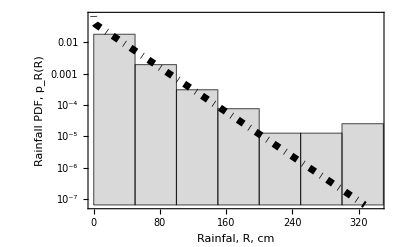

1.51882

1.04496

USGS site 7375000

0.066137

{{BI→0.547771,w→203.623,μ→0.352322,β→0.9}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.535188

K Statistics is 0.0342427

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

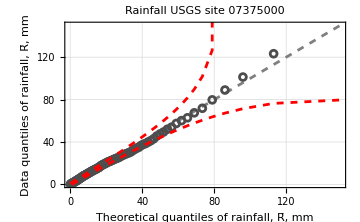

{{1}}

K Statistics is 0.0342427

FindRoot::reged: The point {0.} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.38778×10^-17} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

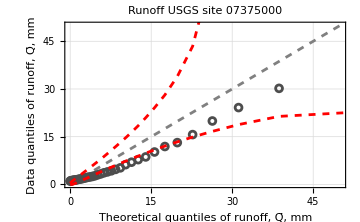

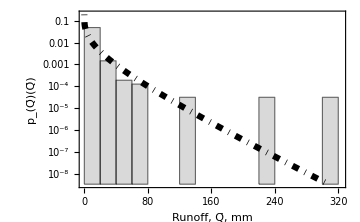

```mathematica
site =15;
eventRunoffsite = DeleteCases[eventRunoff[[All,site+1]],""]*10;
eventRainfallsite = DeleteCases[eventRainfall[[All,site+1]],""]*10;
selectedRow=hydroParameters[[site]];
Clear[ω,α1, α2]
params  =
FindDistributionParameters[eventRainfallsite,HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]]
α=α1 ω+α2(1-ω)/.params;
miny = PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,Max[eventRainfallsite]];
maxy =  PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,0];
prt1 = Histogram[eventRainfallsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRainfallsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=Plot[PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,x],{x,0,Max[eventRainfallsite]},PlotStyle->{DotDashed, Black, Thickness[.0125]},PlotRange->{0,2},ScalingFunctions->{"Linear","Log"}] ;
Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Rainfal, R, cm","Rainfall PDF, p_R(R)"},LabelStyle->{12, Bold}]
EToR=selectedRow["<ET/R>"];
QboQf =selectedRow["<Qb/Qf>"];
σQ2 = selectedRow["sigmaQ^2(cm^2)"]
DI = selectedRow["DI_mean"]
Print["USGS site ",selectedRow["usgs_site_no"]]
α1=α1/.params;
α2=α2/.params;
ω=ω/.params;
α = α1 ω+α2(1-ω);
(*Avg. Runoff from the data, I don't use the event aggregation because it doesn't capture all the runoff*)
QavgD = α(1-EToR)(1-QboQf);
(*Runoff Additive Adjustment Factor, to adjust the runoff avg to the observations*)
Qf = QavgD -Mean[eventRunoffsite]
eventRunoffsiteScaled = Qf +eventRunoffsite;
SelectedansArrayWithBeta= {{BI->0.547771306,w->20.36234966*10,μ->0.352321713,β->0.9}}


n=Length[eventRainfallsite];
rainfallSortedData=Sort[eventRainfallsite];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray={Append[Range[.01,.99,0.01],Max[quantiles*1.0]]};
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
rainfallSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
dist = HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params;
TheoreticalValuesArray ={Table[x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,Flatten[TheoreticalQuantilesArray]}]};

rmse=Sqrt[Mean[(TheoreticalValuesArray[[1]]-EmpiricalValuesArray[[1]])^2]];
rmse/√Variance[rainfallSortedData]

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

probUpper = (TheoreticalQuantilesArray[[1]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[1]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[1]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[1]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)
quantilesUpper =Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbUpper}];
quantilesLower=Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbLower}];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*5]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[1]]],Max[Re[TheoreticalValuesArray[[1]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[1]]],Flatten[EmpiricalValuesArray[[1]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRainfall1 = Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,15*10},{0,15*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[1]]]},{0,Max[EmpiricalValuesArray[[1]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of rainfall, R̄, mm","Data quantiles of rainfall, R̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Rainfall USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium,Background->None]


posToSelect={{1}}

n=Length[eventRunoffsiteScaled];
runoffSortedData=Sort[eventRunoffsiteScaled];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray=Table[
(*Find the closest quantile and corresponding value*)
Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]],{ans,SelectedansArrayWithBeta}];
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
runoffSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
(*Add a small value of .0001 to teh initial quantile to avoid zero as the runoff value in the percent bias comparisons*)
TheoreticalValuesArray =Table[Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,Evaluate[Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]]]}],{ans,SelectedansArrayWithBeta}];

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

(*TheoreticalQuantilesArrayB=Table[
(*Find the closest quantile and corresponding value*)
(Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.001],Max[quantiles*1.0]]),{ans,SelectedansArrayWithBeta}];*)
(*TheoreticalValuesB =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1},AccuracyGoal->2],{P,(TheoreticalQuantilesArrayB[[Flatten[posToSelect]]]//Flatten)}]]*)
probUpper = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)

quantilesUpper =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbUpper}]];
quantilesLower= With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbLower}]];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*6]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[Flatten[posToSelect]]]],Max[Re[TheoreticalValuesArray[[Flatten[posToSelect]]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]],Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRunoff1 =Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,5*10},{0,5*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[Flatten[posToSelect]]]]},{0,Max[EmpiricalValuesArray[[Flatten[posToSelect]]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of runoff, Q̄, mm","Data quantiles of runoff, Q̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Runoff USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium]

miny =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[Max[eventRunoffsite]/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
maxy =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[0/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
prt1 = Histogram[eventRunoffsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRunoffsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pqm[Q/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans,{Q,0,Max[eventRunoffsite]},ScalingFunctions->{"Linear","Log"},PlotStyle->{DotDashed, Black, Thickness[.0125]}]];
QPDFPlot1 = Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Runoff, Q̄, mm","p_(Q̄)(Q̄)"},LabelStyle->{Textsize, Bold},ImageSize->Medium]
```

```mathematica
Max[eventRunoffsite]
```

307.403

### Another Site for LWI

{ω→0.0341145,α1→71.9115,α2→23.0215}

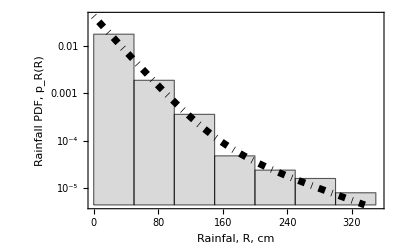

1.75885

0.95185

USGS site 2481000

0.130568

{{BI→0.316037,w→297.509,μ→0.082019,β→0.8}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0756626

K Statistics is 0.0271947

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

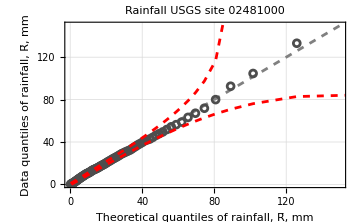

{{1}}

K Statistics is 0.0271947

FindRoot::reged: The point {0.} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

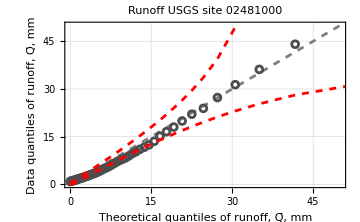

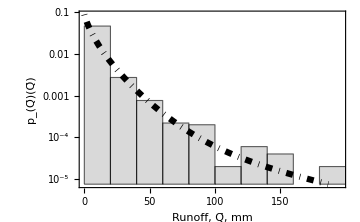

```mathematica
site =17;
eventRunoffsite = DeleteCases[eventRunoff[[All,site+1]],""]*10;
eventRainfallsite = DeleteCases[eventRainfall[[All,site+1]],""]*10;
selectedRow=hydroParameters[[site]];
Clear[ω,α1, α2]
params  =
FindDistributionParameters[eventRainfallsite,HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]]
α=α1 ω+α2(1-ω)/.params;
miny = PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,Max[eventRainfallsite]];
maxy =  PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,0];
prt1 = Histogram[eventRainfallsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRainfallsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=Plot[PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,x],{x,0,Max[eventRainfallsite]},PlotStyle->{DotDashed, Black, Thickness[.0125]},PlotRange->{0,2},ScalingFunctions->{"Linear","Log"}] ;
Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Rainfal, R, cm","Rainfall PDF, p_R(R)"},LabelStyle->{12, Bold}]
EToR=selectedRow["<ET/R>"];
QboQf =selectedRow["<Qb/Qf>"];
σQ2 = selectedRow["sigmaQ^2(cm^2)"]
DI = selectedRow["DI_mean"]
Print["USGS site ",selectedRow["usgs_site_no"]]
α1=α1/.params;
α2=α2/.params;
ω=ω/.params;
α = α1 ω+α2(1-ω);
(*Avg. Runoff from the data, I don't use the event aggregation because it doesn't capture all the runoff*)
QavgD = α(1-EToR)(1-QboQf);
(*Runoff Additive Adjustment Factor, to adjust the runoff avg to the observations*)
Qf = QavgD -Mean[eventRunoffsite]
eventRunoffsiteScaled = Qf +eventRunoffsite;
SelectedansArrayWithBeta= {{BI->0.316036846,w->29.75090357*10,μ->0.082018977,β->.8}}


n=Length[eventRainfallsite];
rainfallSortedData=Sort[eventRainfallsite];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray={Append[Range[.01,.99,0.01],Max[quantiles*1.0]]};
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
rainfallSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
dist = HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params;
TheoreticalValuesArray ={Table[x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,Flatten[TheoreticalQuantilesArray]}]};

rmse=Sqrt[Mean[(TheoreticalValuesArray[[1]]-EmpiricalValuesArray[[1]])^2]];
rmse/√Variance[rainfallSortedData]

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

probUpper = (TheoreticalQuantilesArray[[1]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[1]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[1]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[1]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)
quantilesUpper =Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbUpper}];
quantilesLower=Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbLower}];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*5]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[1]]],Max[Re[TheoreticalValuesArray[[1]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[1]]],Flatten[EmpiricalValuesArray[[1]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRainfall2 = Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,15*10},{0,15*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[1]]]},{0,Max[EmpiricalValuesArray[[1]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of rainfall, R̄, mm","Data quantiles of rainfall, R̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Rainfall USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium,Background->None]


posToSelect={{1}}

n=Length[eventRunoffsiteScaled];
runoffSortedData=Sort[eventRunoffsiteScaled];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray=Table[
(*Find the closest quantile and corresponding value*)
Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]],{ans,SelectedansArrayWithBeta}];
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
runoffSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
(*Add a small value of .0001 to teh initial quantile to avoid zero as the runoff value in the percent bias comparisons*)
TheoreticalValuesArray =Table[Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,Evaluate[Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]]]}],{ans,SelectedansArrayWithBeta}];

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

(*TheoreticalQuantilesArrayB=Table[
(*Find the closest quantile and corresponding value*)
(Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.001],Max[quantiles*1.0]]),{ans,SelectedansArrayWithBeta}];*)
(*TheoreticalValuesB =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1},AccuracyGoal->2],{P,(TheoreticalQuantilesArrayB[[Flatten[posToSelect]]]//Flatten)}]]*)

probUpper = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)

quantilesUpper =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbUpper}]];
quantilesLower= With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbLower}]];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*6]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[Flatten[posToSelect]]]],Max[Re[TheoreticalValuesArray[[Flatten[posToSelect]]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]],Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRunoff2 =Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,5*10},{0,5*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[Flatten[posToSelect]]]]},{0,Max[EmpiricalValuesArray[[Flatten[posToSelect]]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of runoff, Q̄, mm","Data quantiles of runoff, Q̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Runoff USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium]

miny =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[Max[eventRunoffsite]/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
maxy =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[0/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
prt1 = Histogram[eventRunoffsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRunoffsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pqm[Q/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans,{Q,0,Max[eventRunoffsite]},ScalingFunctions->{"Linear","Log"},PlotStyle->{DotDashed, Black, Thickness[.0125]}]];
QPDFPlot2 = Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Runoff, Q̄, mm","p_(Q̄)(Q̄)"},LabelStyle->{Textsize, Bold},ImageSize->Medium]
```

## Load Data From Florida

```mathematica
SetDirectory[NotebookDirectory[]<>"Data"];
hydroParametersImport=Import["USGS_gage_hydro_variables_jacksonville.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParameters=AssociationThread[columnNames->#]&/@dataRows;

eventRunoffImport=Import["USGS_gage_event_runoff_jacksonville.csv"];
columnNames=eventRunoffImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRunoffImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRunoff=AssociationThread[columnNames->#]&/@dataRows;

eventRainfallImport=Import["USGS_gage_event_rainfall_jacksonville.csv"];
columnNames=eventRainfallImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRainfallImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRainfall=AssociationThread[columnNames->#]&/@dataRows;
```

{ω→0.964421,α1→18.762,α2→0.340573}

General::munfl: Exp[-715.545] is too small to represent as a normalized machine number; precision may be lost.

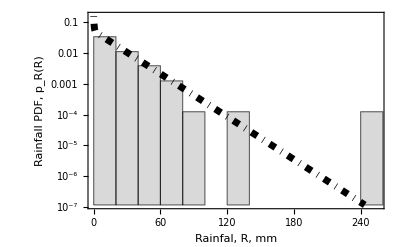

0.961749

1.14271

USGS site 2232415

0.178579

{{BI→0.0593874,w→402.669,μ→0.0231771,β→0.2}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

0.636724

K Statistics is 0.0675681

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

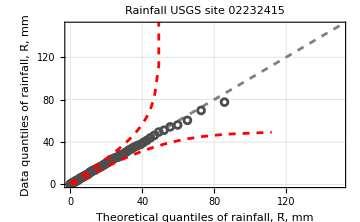

{{1}}

K Statistics is 0.0675681

FindRoot::reged: The point {0.} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

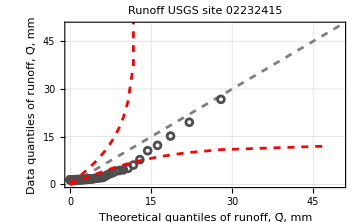

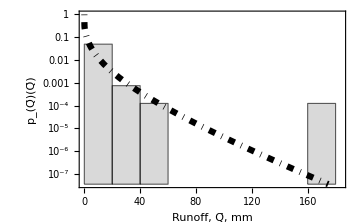

```mathematica
site =15;
eventRunoffsite = DeleteCases[eventRunoff[[All,site+1]],""]*10;
eventRainfallsite = DeleteCases[eventRainfall[[All,site+1]],""]*10;
selectedRow=hydroParameters[[site]];
Clear[ω,α1, α2]
params  =
FindDistributionParameters[eventRainfallsite,HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]]
α=α1 ω+α2(1-ω)/.params;
miny = PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,Max[eventRainfallsite]];
maxy =  PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,0];
prt1 = Histogram[eventRainfallsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRainfallsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=Plot[PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,x],{x,0,Max[eventRainfallsite]},PlotStyle->{DotDashed, Black, Thickness[.0125]},PlotRange->{0,2},ScalingFunctions->{"Linear","Log"}] ;
Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Rainfal, R, mm","Rainfall PDF, p_R(R)"},LabelStyle->{12, Bold}]
EToR=selectedRow["<ET/R>"];
QboQf =selectedRow["<Qb/Qf>"];
σQ2 = selectedRow["sigmaQ^2(cm^2)"]
DI = selectedRow["DI_mean"]
Print["USGS site ",selectedRow["usgs_site_no"]]
α1=α1/.params;
α2=α2/.params;
ω=ω/.params;
α = α1 ω+α2(1-ω);
(*Avg. Runoff from the data, I don't use the event aggregation because it doesn't capture all the runoff*)
QavgD = α(1-EToR)(1-QboQf);
(*Runoff Additive Adjustment Factor, to adjust the runoff avg to the observations*)
Qf = QavgD -Mean[eventRunoffsite]
eventRunoffsiteScaled = Qf +eventRunoffsite;
SelectedansArrayWithBeta= {{BI->0.059387431,w->40.26687443*10,μ->0.023177074,β->0.2}}


n=Length[eventRainfallsite];
rainfallSortedData=Sort[eventRainfallsite];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray={Append[Range[.01,.99,0.01],Max[quantiles*1.0]]};
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
rainfallSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
dist = HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params;
TheoreticalValuesArray ={Table[x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,Flatten[TheoreticalQuantilesArray]}]};

rmse=Sqrt[Mean[(TheoreticalValuesArray[[1]]-EmpiricalValuesArray[[1]])^2]];
rmse/√Variance[rainfallSortedData]

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

probUpper = (TheoreticalQuantilesArray[[1]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[1]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[1]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[1]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)
quantilesUpper =Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbUpper}];
quantilesLower=Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbLower}];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*5]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[1]]],Max[Re[TheoreticalValuesArray[[1]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[1]]],Flatten[EmpiricalValuesArray[[1]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRainfall3 = Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,15*10},{0,15*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[1]]]},{0,Max[EmpiricalValuesArray[[1]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of rainfall, R̄, mm","Data quantiles of rainfall, R̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Rainfall USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium,Background->None]


posToSelect={{1}}

n=Length[eventRunoffsiteScaled];
runoffSortedData=Sort[eventRunoffsiteScaled];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray=Table[
(*Find the closest quantile and corresponding value*)
Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]],{ans,SelectedansArrayWithBeta}];
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
runoffSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
(*Add a small value of .0001 to teh initial quantile to avoid zero as the runoff value in the percent bias comparisons*)
TheoreticalValuesArray =Table[Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,Evaluate[Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]]]}],{ans,SelectedansArrayWithBeta}];

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

(*TheoreticalQuantilesArrayB=Table[
(*Find the closest quantile and corresponding value*)
(Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.001],Max[quantiles*1.0]]),{ans,SelectedansArrayWithBeta}];*)
(*TheoreticalValuesB =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1},AccuracyGoal->2],{P,(TheoreticalQuantilesArrayB[[Flatten[posToSelect]]]//Flatten)}]]*)

probUpper = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)

quantilesUpper =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbUpper}]];
quantilesLower= With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbLower}]];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*6]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[Flatten[posToSelect]]]],Max[Re[TheoreticalValuesArray[[Flatten[posToSelect]]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]],Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRunoff3 =Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,5*10},{0,5*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[Flatten[posToSelect]]]]},{0,Max[EmpiricalValuesArray[[Flatten[posToSelect]]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of runoff, Q̄, mm","Data quantiles of runoff, Q̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Runoff USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium]

miny =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[Max[eventRunoffsite]/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
maxy =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[0/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
prt1 = Histogram[eventRunoffsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRunoffsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pqm[Q/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans,{Q,0,Max[eventRunoffsite]},ScalingFunctions->{"Linear","Log"},PlotStyle->{DotDashed, Black, Thickness[.0125]}]];
QPDFPlot3= Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Runoff, Q̄, mm","p_(Q̄)(Q̄)"},LabelStyle->{Textsize, Bold},ImageSize->Medium]
```

### Another site for Florida

{ω→1.,α1→22.5131,α2→4.23705}

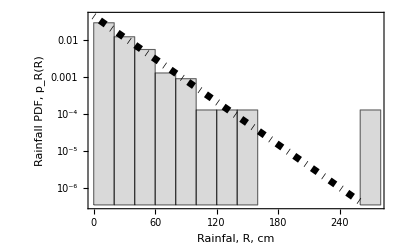

1.70904

1.11552

USGS site 2246459

0.617072

{{BI→0.298165,w→390.427,μ→0.00357318,β→0.4}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.542889

K Statistics is 0.0691255

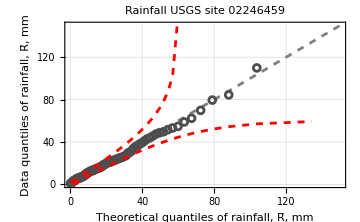

{{1}}

K Statistics is 0.0691255

FindRoot::reged: The point {-1.38778×10^-17} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

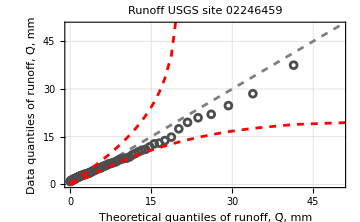

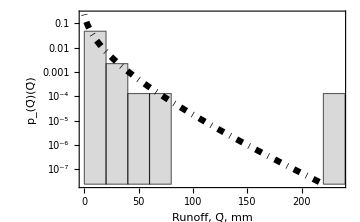

```mathematica
site =49(*37*);
eventRunoffsite = DeleteCases[eventRunoff[[All,site+1]],""]*10;
eventRainfallsite = DeleteCases[eventRainfall[[All,site+1]],""]*10;
selectedRow=hydroParameters[[site]];
Clear[ω,α1, α2]
params  =
FindDistributionParameters[eventRainfallsite,HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]]
α=α1 ω+α2(1-ω)/.params;
miny = PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,Max[eventRainfallsite]];
maxy =  PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,0];
prt1 = Histogram[eventRainfallsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRainfallsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=Plot[PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,x],{x,0,Max[eventRainfallsite]},PlotStyle->{DotDashed, Black, Thickness[.0125]},PlotRange->{0,2},ScalingFunctions->{"Linear","Log"}] ;
Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Rainfal, R, cm","Rainfall PDF, p_R(R)"},LabelStyle->{Textsize, Bold}]
EToR=selectedRow["<ET/R>"];
QboQf =selectedRow["<Qb/Qf>"];
σQ2 = selectedRow["sigmaQ^2(cm^2)"]
DI = selectedRow["DI_mean"]
Print["USGS site ",selectedRow["usgs_site_no"]]
α1=α1/.params;
α2=α2/.params;
ω=ω/.params;
α = α1 ω+α2(1-ω);
(*Avg. Runoff from the data, I don't use the event aggregation because it doesn't capture all the runoff*)
QavgD = α(1-EToR)(1-QboQf);
(*Runoff Additive Adjustment Factor, to adjust the runoff avg to the observations*)
Qf = QavgD -Mean[eventRunoffsite]
eventRunoffsiteScaled = Qf +eventRunoffsite;
SelectedansArrayWithBeta= {{BI->0.298164957,w->39.04274258*10,μ->0.003573183,β->0.4}}
(*SelectedansArrayWithBeta= {{BI->0.213755796,w->35.88992682,μ->0.036378103,β->0.01}}*)



n=Length[eventRainfallsite];
rainfallSortedData=Sort[eventRainfallsite];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray={Append[Range[.01,.99,0.01],Max[quantiles*1.0]]};
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
rainfallSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
dist = HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params;
TheoreticalValuesArray ={Table[x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,Flatten[TheoreticalQuantilesArray]}]};

rmse=Sqrt[Mean[(TheoreticalValuesArray[[1]]-EmpiricalValuesArray[[1]])^2]];
rmse/√Variance[rainfallSortedData]

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

probUpper = (TheoreticalQuantilesArray[[1]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[1]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[1]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[1]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)
quantilesUpper =Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbUpper}];
quantilesLower=Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbLower}];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*5]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[1]]],Max[Re[TheoreticalValuesArray[[1]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[1]]],Flatten[EmpiricalValuesArray[[1]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRainfall4= Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,15*10},{0,15*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[1]]]},{0,Max[EmpiricalValuesArray[[1]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of rainfall, R̄, mm","Data quantiles of rainfall, R̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Rainfall USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium,Background->None]


posToSelect={{1}}

n=Length[eventRunoffsiteScaled];
runoffSortedData=Sort[eventRunoffsiteScaled];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray=Table[
(*Find the closest quantile and corresponding value*)
Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]],{ans,SelectedansArrayWithBeta}];
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
runoffSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
(*Add a small value of .0001 to teh initial quantile to avoid zero as the runoff value in the percent bias comparisons*)
TheoreticalValuesArray =Table[Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,Evaluate[Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]]]}],{ans,SelectedansArrayWithBeta}];

(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

(*TheoreticalQuantilesArrayB=Table[
(*Find the closest quantile and corresponding value*)
(Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.001],Max[quantiles*1.0]]),{ans,SelectedansArrayWithBeta}];*)
(*TheoreticalValuesB =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1},AccuracyGoal->2],{P,(TheoreticalQuantilesArrayB[[Flatten[posToSelect]]]//Flatten)}]]*)

probUpper = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)

quantilesUpper =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbUpper}]];
quantilesLower= With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbLower}]];

BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*6]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[Flatten[posToSelect]]]],Max[Re[TheoreticalValuesArray[[Flatten[posToSelect]]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]],Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
QQplotRunoff4 =Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,5*10},{0,5*10}}(*PlotRange->{{0,Max[TheoreticalValuesArray[[Flatten[posToSelect]]]]},{0,Max[EmpiricalValuesArray[[Flatten[posToSelect]]]]}}*),Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of runoff, Q̄, mm","Data quantiles of runoff, Q̄, mm"},LabelStyle->{Textsize, Bold},PlotLabel->StringJoin["Runoff USGS site ","0" <>ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium]

miny =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[Max[eventRunoffsite]/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
maxy =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[0/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
prt1 = Histogram[eventRunoffsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRunoffsite]*1.07},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pqm[Q/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans,{Q,0,Max[eventRunoffsite]},ScalingFunctions->{"Linear","Log"},PlotStyle->{DotDashed, Black, Thickness[.0125]}]];
QPDFPlot4= Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Runoff, Q̄, mm","p_(Q̄)(Q̄)"},LabelStyle->{Textsize, Bold},ImageSize->Medium]
```

```mathematica
(*Function to add a label in the upper-left corner of a plot*)
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{0,.5}]]}]]
```

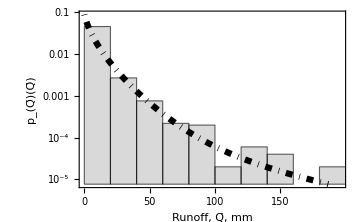
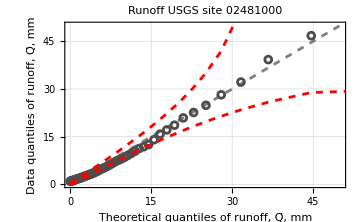
-Graphics-a) | -Graphics- | -Graphics-
-Graphics-b) | -Graphics- | -Graphics-
-Graphics-c) | -Graphics- | -Graphics-
-Graphics-d) | -Graphics- | -Graphics-

```mathematica
(*Function to add a label in the upper-left corner of a plot*)
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{0,1.1}]]}]]
(*Function to add a label in the upper-left frame corner*)
labeledPlot[fig_,label_]:=Overlay[{fig,Style[label,Bold,16]},Alignment->{Left,Top},BaseStyle->{ImageMargins->0}]
(*Grid with labeled figures*)
grid=Grid[{{labeledPlot[QQplotRainfall1 ,"a)"],QPDFPlot1 ,QQplotRunoff1 },{labeledPlot[QQplotRainfall2 ,"b)"],QPDFPlot2 ,QQplotRunoff2 },{labeledPlot[QQplotRainfall3 ,"c)"],QPDFPlot3 ,QQplotRunoff3 },{labeledPlot[QQplotRainfall4 ,"d)"],QPDFPlot4 ,QQplotRunoff4}},Spacings->2]
```

```mathematica
(*Export the grid as EPS*)
SetDirectory[NotebookDirectory[]<>"Data"];
Export["Figure9.eps",grid]
```

Fig.X.2.eps